```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
threshold=0;maxtime=500;
case=1;
Switch[case,
1,C0=1;C1=0.75;T=60;τ2=0.5;τ4=1
(*1,C0=1;C1=0.75;T=30;τ2=0.4;τ4=1;,
3,C0=1;C1=0.85;T=100;τ2=0.4;τ4=1;,
4,C0=1;C1=0.75;T=200;τ2=0.4;τ4=1;*)
];
filename=StringJoin["Fig7_HH_",ToString[T],"_C1_",ToString[C1],".png"];
(*(*HH Parameters from https://www.st-andrews.ac.uk/~wjh/hh_model_intro/, Doesnt seem to be stimulated*)
αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Voffset =-65;
Vrest=0;
mrest=0.05;
hrest=0.596;
nrest=0.315;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;*)
(*HH Parameters from Weinberg*)
αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Vrest=-65; (*Weinberg uses -80, but it seems to be *)
mrest=0.05;
hrest=0.596;
nrest=0.315;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;

(*Ionic Chanels*)
Am[V_]=αm (V-Vαm)/(1-Exp[-(V-Vαm)/Kαm]);
Bm[V_]=βm Exp[-(V-Vβm)/Kβm];
Ah[V_]=αh Exp[-(V-Vαh)/Kαh];
Bh[V_]=βh/(1+Exp[-(V-Vβh)/Kβh]);
An[V_]=αn (V-Vαn)/(1-Exp[-(V-Vαn)/Kαn]);
Bn[V_]=βn Exp[-(V-Vβn)/Kβn];
```

```mathematica
(*Solving HH*)
fRateHH={};
fRateHHs={};
simulation={};
Do[Do[
(*Define capacitance function*)
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(C1-C0)(Mod[t,T]-τ1 T)/((τ2-τ1)T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T] - τ3 T)(C0-C1)/((τ4-τ3)T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/((τ2-τ1)T),Mod[t,T]< τ3 T,0, True,(C0-C1)/((τ4-τ3)T)];
(*Solving HH*)
{U,M,H,NN}=NDSolveValue[{u'[t]==-gNa m[t]^3 h[t](u[t]/Ct[t]-Vrest-ENa)-gK n[t]^4(u[t]/Ct[t]-Vrest-EK) -gL(u[t]/Ct[t]-Vrest-EL),
m'[t]==Am[u[t]/Ct[t]-Vrest](1-m[t])-Bm[u[t]/Ct[t]-Vrest]m[t],
h'[t]==Ah[u[t]/Ct[t]-Vrest](1-h[t])-Bh[u[t]/Ct[t]-Vrest] h[t],
n'[t]==An[u[t]/Ct[t]-Vrest](1-n[t])-Bn[u[t]/Ct[t]-Vrest]n[t],
u[0]==Ct[0]*Vrest,m[0]==mrest,h[0]==hrest,n[0]==nrest},
{u,m,h,n},{t,0,maxtime}];

peaksHH = FindPeaks[Table[U[t]/Ct[t],{t,0,maxtime,1}],2,0,threshold];
(*peaksHH = FindPeaks[Table[V[t],{t,0,maxtime,1}],0,0,threshold];*)
countHH=Length[peaksHH];
pointHH = {τ1,τ3,N[countHH/maxtime *1000]};
fRateHH = Append[fRateHH,pointHH];
,{τ1,0.2,0.498,0.02}],{τ3,0.7,0.998,0.02}];
```

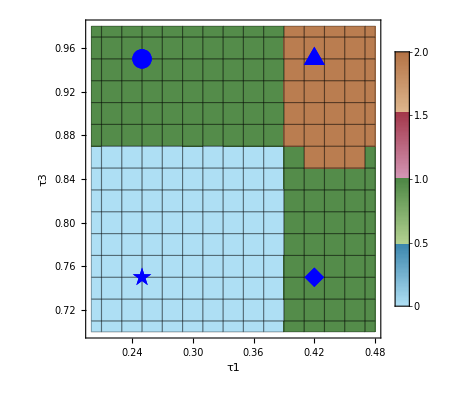

Fig7_HH_60_C1_0.75.png

```mathematica
(*Visualization*)
extract=fRateHH[[All,{1,2,3}]];
extract=extract.{{1,0,0},{0,1,0},{0,0,T/1000}};
g1= ListDensityPlot[extract,
Mesh->All,
InterpolationOrder->0,
PlotLegends->BarLegend[{Automatic,{0,2}}],
PlotLegends->Automatic,
PlotRange->{Full,Full,{0,2}},
PlotRangeClipping->False,
ColorFunction->(ColorData["DarkBands"][0.65*#/2]&),
ColorFunctionScaling->False,
FrameLabel->{"τ1","τ3"},
LabelStyle->Directive[Black,FontSize->16]
];
g2=ListPlot[{{{0.25,0.95}},{{0.42,0.95}},{{0.25,0.75}},{{0.42,0.75}}},
PlotMarkers->{
Style["●",Blue,20],
Style["▲",Blue,25],
Style["★",Blue,20],
Style["◆",Blue,20]}];
g3=Show[g1,g2]
Export[filename,g3]
```